## Replicator Dynamics - three player game

### Simplex Plot

```mathematica
(* Geometric transformation to simplex *)
{err,trans}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
(* Edges of simplex *)
triangle=Graphics[{Thickness[0.005],Darker[Gray],GeometricTransformation[Line[{{0,0},{0,1},{1,0},{0,0}}],trans]}];
(* Some random data *)
dummyData=Select[RandomReal[1,{100,2}],Total[#]<=1&];
(* Plot the points *)
points=ListPlot[dummyData,PlotStyle->PointSize[0.03]];
(* Or plot the lines *)
lines=ListLinePlot[dummyData,PlotStyle->Black];
(* Show all together *)
(* The trick is to extract the "First" part of the plots, and transform it *)
```

### Plotting

```mathematica
originalgamematrix={{{17.6,-19,0.85},{-7,12.7,10},{-16.25,-11.2,2}},{{0.8,-19,0.85},{12.65,-10,20},{8.25,2.8,-9}},{{-2,2,-1},{1,2,1},{-1,1,0}}};
(*transformedmatrix={{{19.6,-21,1.85},{-8,10.7,9},{-15.25,-12.2,2}},{{2.8,-21,1.85},{11.65,-12,19},{9.25,1.8,-9}},{{0,0,0},{0,0,0},{0,0,0}}};
transformedmatrix2={{{19.6,-21,0},{-8,10.7,0},{-13.4,-3.2,2}},{{2.8,-21,1.85},{11.65,-12,19},{9.25,1.8,-9}},{{0,0,0},{0,0,0},{0,0,0}}};*)
```

```mathematica
payoffs=transformedmatrix2;
fits[x_,y_]:=Table[∑_(j=1)^3 (∑_(k=1)^3 (payoffs⟦i,j,k⟧ Subscript[x, j] Subscript[x, k])),{i,1,3}]/.{Subscript[x, 1]->x,Subscript[x, 2]->y,Subscript[x, 3]->1-x-y};
```

```mathematica
π1[x_,y_,z_]:=fits[x,y]⟦1⟧;

π2[x_,y_,z_]:=fits[x,y]⟦2⟧;

π3[x_,y_,z_]:=fits[x,y]⟦3⟧;
πbar[x_,y_,z_]:=x π1[x,y,z]+y π2[x,y,z]+z π3[x,y,z];
dx[x_, y_, z_]:=x(π1[x,y,z]-πbar[x,y,z]);
dy[x_, y_, z_]:=y(π2[x,y,z]-πbar[x,y,z]);
dz[x_, y_, z_]:=z(π3[x,y,z]-πbar[x,y,z]);

Fermi[x_]:={
dx[x⟦1⟧,x⟦2⟧, x⟦3⟧],
dy[x⟦1⟧,x⟦2⟧, x⟦3⟧],
dz[x⟦1⟧,x⟦2⟧, x⟦3⟧]
}
x=.;y=.;z=1-x-y;
fa=fits[x,y]⟦1⟧;
fb=fits[x,y]⟦2⟧;
fc=fits[x,y]⟦3⟧;
```

```mathematica
x=.
y=.
sol=NSolve[{dx[x,y,1-x-y]==0,dy[x,y,1-x-y]==0},{x,y},Reals];
```

```mathematica
data={x,y}/.sol;
relData=Select[data,Total[#]<=1&&Total[#]≥0&];
p1=ListPlot[relData,PlotStyle->{Black,PointSize[0.03]}];
p2=ListPlot[relData,PlotStyle->{White,PointSize[0.015]}];
p3=ListPlot[{{1,0},{0,1},{0,0}},PlotStyle->{Red,PointSize[0.03]}];
p4=ListPlot[{{1,0},{0,1},{0,0}},PlotStyle->{White,PointSize[0.015]}];
points=Show[p1,p2,p3,p4];
```

{{1.,0.},{0.49745,0.314111},{0.,1.},{0.118732,0.456688},{0.371639,0.0378092},{0.316725,0.},{0.,0.473684},{0.0807156,0.345594},{0.,0.454545},{0.180418,0.},{0.,0.}}

Plotting  isoclines

```mathematica
eq1=fa-fc;
eq2=fb-fc;
```

```mathematica
cplt=ContourPlot[eq1==0,{x,0,1},{y,0,1},RegionFunction->Function[{x,y},x+y≤1],PlotRange->All,ContourStyle->Darker[Red]];
cplt2=ContourPlot[eq2==0,{x,0,1},{y,0,1},RegionFunction->Function[{x,y},x+y≤1],PlotRange->All,ContourStyle->Darker[Blue]];
```

```mathematica
sp=StreamDensityPlot[{dx[x,y,1-x-y],dy[x,y,1-x-y]},{x,0,1},{y,0,1},Frame->True,ColorFunction->"Pastel",ColorFunctionScaling->False,StreamStyle->Darker[Gray],StreamColorFunction->None,StreamPoints->Fine,StreamMarkers-> {"PinDart"},StreamScale->Large,RegionFunction->Function[{x,y,vx,vy,n},x +y≤1&&x≥0&&y≥0]];
```

```mathematica
trajdata=NDSolve[{x'[t]==dx[x[t],y[t],1-x[t]-y[t]],y'[t]==dy[x[t],y[t],1-x[t]-y[t]],x[0]==0.45,y[0]==0.08},{x,y},{t,0,50}];
parpl=ParametricPlot[Evaluate[{x[t],y[t]}/.trajdata],{t,0,50},PlotRange->All,PlotStyle->Directive[Black,Dashed]];
```

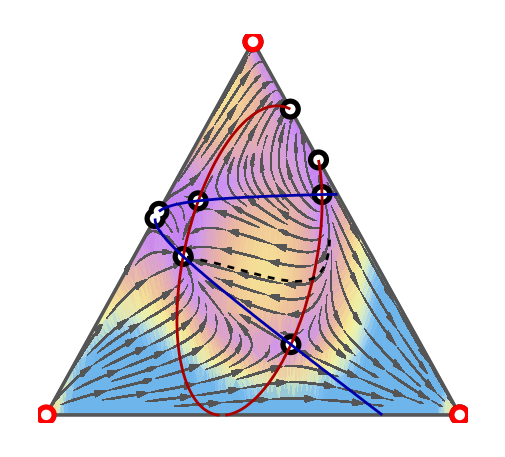

```mathematica
psim=Show[
Graphics[GeometricTransformation[First[Show[sp]],trans]],triangle,Graphics[GeometricTransformation[First[Show[points]],trans]],
Graphics[GeometricTransformation[First[Show[cplt,cplt2]],trans]],
Graphics[GeometricTransformation[First[parpl],trans]](*,
Graphics[GeometricTransformation[Text["label",{0,1}],trans]]*)
]
```

## Equivalent Lotka Volterra system

Use  the game from above but call it A for ease

```mathematica
A=originalgamematrix;
```

```mathematica
A//MatrixForm
```

((17.6
-19
0.85) | (-7
12.7
10) | (-16.25
-11.2
2)
(0.8
-19
0.85) | (12.65
-10
20) | (8.25
2.8
-9)
(-2
2
-1) | (1
2
1) | (-1
1
0))

The  number of species is one less than the number of strategies

```mathematica
n=3;m=n-1;
```

### Transformation

First create a nxnxn matrix of zeros

```mathematica
Table[Subscript[b, i,j,k]=0,{i,1,n},{j,1,n},{k,1,n}];
```

Now we fill in the growth rates

```mathematica
Table[Subscript[b, i,n,n]=A⟦i,n,n⟧-A⟦n,n,n⟧,{i,1,2,1}]
```

{2,-9}

Now we include the payoffs for the linear interactions for strategy 1

```mathematica
Table[Subscript[b, 1,j,n]=A⟦1,j,n⟧-A⟦n,j,n⟧,{j,1,m,1}]
Table[Subscript[b, 1,n,k]=A⟦1,n,k⟧-A⟦n,n,k⟧,{k,1,m,1}]
```

{1.85,9}

{-15.25,-12.2}

Now we include the payoffs for the nonlinear interactions for strategy 1

```mathematica
Table[Subscript[b, 1,j,k]=A⟦1,j,k⟧-A⟦n,j,k⟧,{k,1,m,1},{j,1,m,1}]
```

{{19.6,-8},{-21,10.7}}

Now we include the payoffs for the linear interactions for strategy 2

```mathematica
Table[Subscript[b, 2,j,n]=A⟦2,j,n⟧-A⟦n,j,n⟧,{j,1,m,1}]
Table[Subscript[b, 2,n,k]=A⟦2,n,k⟧-A⟦n,n,k⟧,{k,1,m,1}]
```

{1.85,19}

{9.25,1.8}

Now we include the payoffs for the nonlinear interactions for strategy 2

```mathematica
Table[Subscript[b, 2,j,k]=A⟦2,j,k⟧-A⟦n,j,k⟧,{k,1,m,1},{j,1,m,1}]
```

{{2.8,11.65},{-21,-12}}

Collect all in matrix B

```mathematica
B=Table[Subscript[b, i,j,k],{i,1,n},{j,1,n},{k,1,n}]
```

{{{19.6,-21,1.85},{-8,10.7,9},{-15.25,-12.2,2}},{{2.8,-21,1.85},{11.65,-12,19},{9.25,1.8,-9}},{{0,0,0},{0,0,0},{0,0,0}}}

```mathematica
B//MatrixForm
```

((19.6
-21
1.85) | (-8
10.7
9) | (-15.25
-12.2
2)
(2.8
-21
1.85) | (11.65
-12
19) | (9.25
1.8
-9)
(0
0
0) | (0
0
0) | (0
0
0))

```mathematica
lveqs=Table[Subscript[y, i]'[t]==Subscript[y, i][t] ((Subscript[b, i,n,n]-Subscript[b, n,n,n])+∑_(j=1)^m (Subscript[b, i,j,n]-Subscript[b, n,j,n])Subscript[y, j][t]+∑_(k=1)^m (Subscript[b, i,n,k]-Subscript[b, n,n,k])Subscript[y, k][t]+(∑_(j=1)^m ∑_(k=1)^m (Subscript[b, i,j,k]-Subscript[b, n,j,k])Subscript[y, j][t]Subscript[y, k][t])),{i,1,2,1}]
```

{y_1'[t]==y_1[t] (2-13.4 y_1[t]+19.6 y_1[t]^2-3.2 y_2[t]-29 y_1[t] y_2[t]+10.7 y_2[t]^2),y_2'[t]==y_2[t] (-9+11.1 y_1[t]+2.8 y_1[t]^2+20.8 y_2[t]-9.35 y_1[t] y_2[t]-12 y_2[t]^2)}

```mathematica
tmax=100;
Manipulate[lv=NDSolve[{lveqs,
Subscript[y, 1][0]==init,Subscript[y, 2][0]==1-init},{Subscript[y, 1],Subscript[y, 2]},{t,0,tmax}];Plot[Evaluate[{Subscript[y, 1][t],Subscript[y, 2][t]}/.lv],{t,0,tmax},PlotStyle->{Red,Blue},PlotStyle->Automatic,Frame->True,FrameStyle->Directive[Black,Thickness[0.003]],PlotRange->{Automatic,{-0.01,2.8}},FrameLabel->{Style["Time",14],Style["Abundance of species",14]}],{{init,0.5},0,1}]
```

```mathematica
Evaluate[{Subscript[y, 1][tmax],Subscript[y, 2][tmax]}/.lv]
```

{{0.279646,1.07562}}

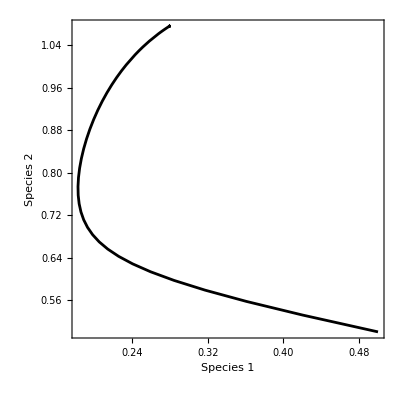

```mathematica
ParametricPlot[Evaluate[{Subscript[y, 1][t],Subscript[y, 2][t]}/.lv],{t,0,tmax},Axes->None,PlotStyle->Black,PlotStyle->Black,PlotStyle->Automatic,Frame->True,FrameStyle->Directive[Black,Thickness[0.004]],PlotRange->Full,FrameLabel->{Style["Species 1",16,RGBColor["#807FFF"]],Style["Species 2",16,RGBColor["#DEAD26"]]},AspectRatio->1]
```